# DateListPlot - set framticks at dates of the data points

```mathematica
data=WolframAlpha["brad pitt",{{"PopularityPod:WikipediaStatsData",1},"TimeSeriesData"}];

rarify=data[[1;;-1;;10]]
```

{{{2007,12,13,0,0,0.},6733.29 hits/day},{{2008,2,21,0,0,0.},8033.29 hits/day},{{2008,5,1,0,0,0.},7289.29 hits/day},{{2008,7,10,0,0,0.},11751.6 hits/day},{{2008,9,18,0,0,0.},10736.4 hits/day},{{2008,11,27,0,0,0.},9911. hits/day},{{2009,2,5,0,0,0.},15607.9 hits/day},{{2009,4,16,0,0,0.},10696.7 hits/day},{{2009,6,25,0,0,0.},12354.9 hits/day},{{2009,9,3,0,0,0.},15445. hits/day},{{2009,11,19,0,0,0.},10671.5 hits/day},{{2010,1,28,0,0,0.},20454.8 hits/day},{{2010,4,8,0,0,0.},11761. hits/day},{{2010,6,17,0,0,0.},6778.5 hits/day},{{2010,8,26,0,0,0.},16495.6 hits/day},{{2010,11,4,0,0,0.},13316.3 hits/day},{{2011,1,13,0,0,0.},16118.7 hits/day},{{2011,3,24,0,0,0.},13893.1 hits/day},{{2011,6,2,0,0,0.},17044.9 hits/day},{{2011,8,11,0,0,0.},14097. hits/day},{{2011,10,20,0,0,0.},11917.4 hits/day},{{2011,12,29,0,0,0.},18309.5 hits/day},{{2012,3,8,0,0,0.},18309.3 hits/day},{{2012,5,17,0,0,0.},13500.6 hits/day},{{2012,7,26,0,0,0.},13914. hits/day},{{2012,10,4,0,0,0.},12223.6 hits/day},{{2012,12,13,0,0,0.},14403.3 hits/day},{{2013,2,21,0,0,0.},15679.7 hits/day},{{2013,5,2,0,0,0.},11578.6 hits/day},{{2013,7,11,0,0,0.},13703. hits/day},{{2013,9,19,0,0,0.},11502.3 hits/day},{{2013,11,28,0,0,0.},10402.6 hits/day},{{2014,2,6,0,0,0.},10518. hits/day},{{2014,4,17,0,0,0.},8728.57 hits/day},{{2014,6,26,0,0,0.},9038.57 hits/day},{{2014,9,4,0,0,0.},13716.7 hits/day},{{2014,11,13,0,0,0.},7773.86 hits/day},{{2015,1,22,0,0,0.},8077.29 hits/day},{{2015,4,2,0,0,0.},6287.43 hits/day},{{2015,6,11,0,0,0.},5766.14 hits/day},{{2015,8,20,0,0,0.},5675.71 hits/day},{{2015,10,29,0,0,0.},5120.43 hits/day},{{2016,1,7,0,0,0.},5928.29 hits/day},{{2016,3,17,0,0,0.},4912.71 hits/day},{{2016,5,26,0,0,0.},4755.14 hits/day}}

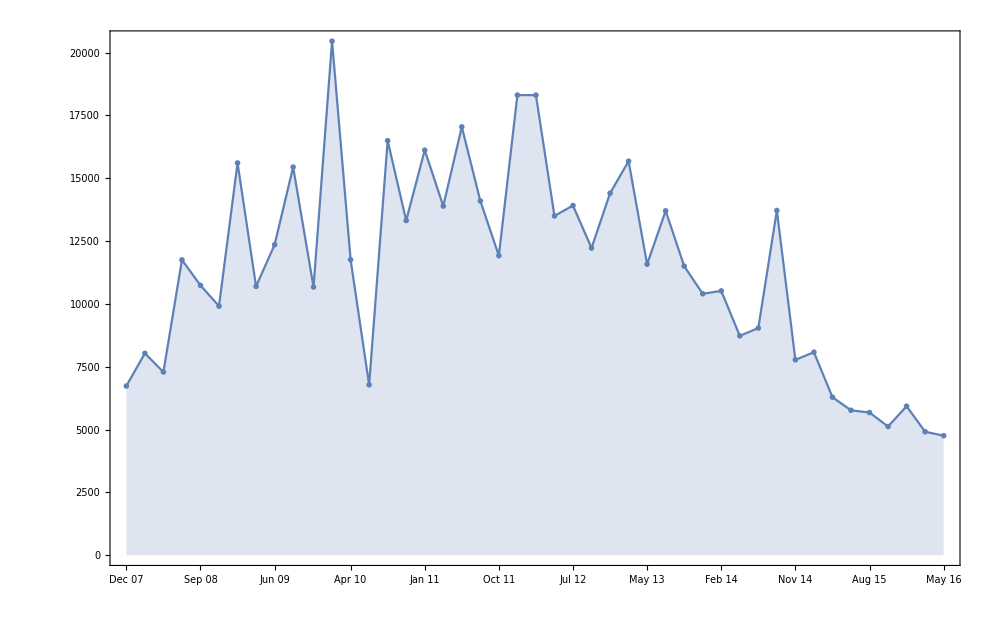

```mathematica
plot=DateListPlot[rarify,FrameTicks->{rarify[[All,1]],Automatic},Filling->Bottom,PlotMarkers->{Automatic,Small},Frame->True,DateTicksFormat->{"MonthNameShort"," ","YearShort"},ImageSize-> 1000]
```

```mathematica
plot/.x:(FrameTicks->_):>(x/.s_String:>Rotate[Style[s,Larger],60 Degree])
```

-Graphics-